```mathematica
SetOptions[EvaluationNotebook[],CommonDefaultFormatTypes->{"Output"->StandardForm}]
```

```mathematica
Needs["PlotLegends`"]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

## Quantum jump in a free 2-level system (1)

```mathematica
(*Dimension less parameter: γ unit, ℏ=1*)
```

```mathematica
(*intial condition of state |ψ[0]⟩={1,0}*)
c={{0,0},{1,0}};(*jumping operator representing decay channel*)
t=3;dt=0.01;
```

```mathematica
H=-ⅈ/2 ConjugateTranspose[c].c;
```

```mathematica
Clear[ψ]
Do[
ψ[0,j]={1,0};For[n=0,n≤t/dt,n++,If[Norm[c.ψ[n,j]]^2 dt>RandomReal[{0,1}],ψ[n+1,j]=(c.ψ[n,j])/Norm[c.ψ[n,j]],ψ[n+1,j]=(ψ[n,j]+H.ψ[n,j]dt)/Norm[ψ[n,j]+H.ψ[n,j]dt]]]
,{j,1,1000}]
Clear[n]
```

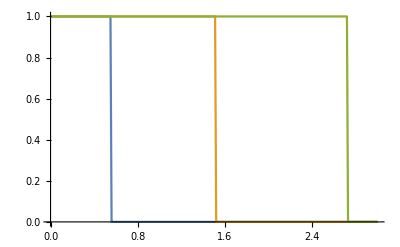

```mathematica
ListPlot[{Table[{n dt,Norm[{1,0}.ψ[n,1]]^2},{n,0,t/dt}],Table[{n dt,Norm[{1,0}.ψ[n,2]]^2},{n,0,t/dt}],Table[{n dt,Norm[{1,0}.ψ[n,3]]^2},{n,0,t/dt}]},Joined->True]
```

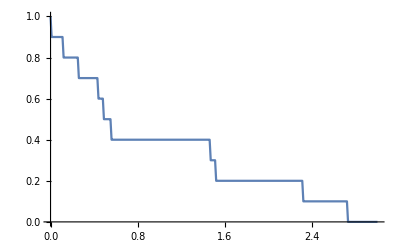

```mathematica
ListPlot[Table[{n dt,Sum[Norm[{1,0}.ψ[n,j]]^2,{j,1,10}]/10},{n,0,t/dt}],Joined->True]
```

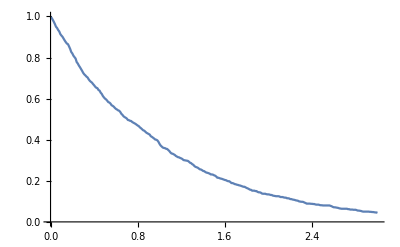

```mathematica
ListPlot[Table[{n dt,Sum[Norm[{1,0}.ψ[n,j]]^2,{j,1,1000}]/1000},{n,0,t/dt}],Joined->True]
```

## Quantum jump in a free 2-level system (2)

```mathematica
Clear[a,b,c,t,dt,num,H]
a=√(2/3);b=√(1/3); (* intial condition of state |ψ⟩ *)
c={{0,1},{0,0}}; (* jumping operator representing decay channel *)
t=10;dt=0.01;
num=1000; (* sample size of the system / size of the ensemble *)
H=-ⅈ/2 ConjugateTranspose[c].c;
```

```mathematica
Clear[ψ]
Monitor[Do[
ψ[0,j]={a,b};For[n=0,n≤t/dt,n++,If[Norm[c.ψ[n,j]]^2 dt>RandomReal[{0,1}],ψ[n+1,j]=(c.ψ[n,j])/Norm[c.ψ[n,j]],ψ[n+1,j]=(ψ[n,j]+H.ψ[n,j]dt)/Norm[ψ[n,j]+H.ψ[n,j]dt]]]
,{j,1,num}];,Row[{ProgressIndicator[j,{1,num}],j}," "]]
Clear[n]
```

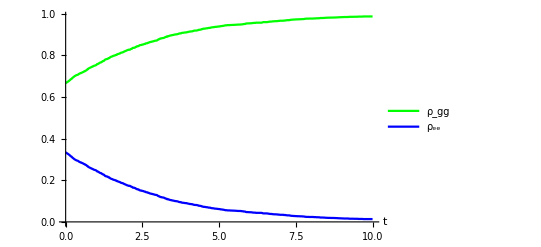

```mathematica
ListPlot[{Table[{n dt,Sum[Norm[{1,0}.ψ[n,j]]^2,{j,1,num}]/num},{n,0,t/dt}],Table[{n dt,Sum[Norm[{0,1}.ψ[n,j]]^2,{j,1,num}]/num},{n,0,t/dt}]},Joined->True,PlotRange->All,PlotStyle->{Green,Blue},AxesLabel->{Style["t",FontFamily->"Times New Roman",FontSize->14]},PlotLegends->{Style["ρ_gg",FontFamily->"Times New Roman"],Style["ρ_ee",FontFamily->"Times New Roman"]}]
```

```mathematica
(* final population *)
tn=IntegerPart[t/dt];
Sum[Norm[{1,0}.ψ[tn,j]]^2,{j,1,num}]/num
Sum[Norm[{0,1}.ψ[tn,j]]^2,{j,1,num}]/num
Clear[tn]
```

0.986444

0.0135565

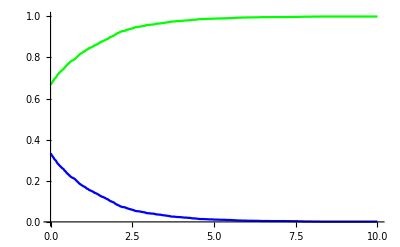
```mathematica
ShowLegend[Show[-Graphics-,PlotRange->{0,1}],{{{Graphics[{Gray,Line[{{0,0},{2,0}}]}],"ρ_ee"},{Graphics[{Blue,Line[{{0,0},{2,0}}]}],"ρ_gg"}},LegendPosition->{0.5,0.2},LegendSize->{0.3,0.2},LegendShadow->False}]
```

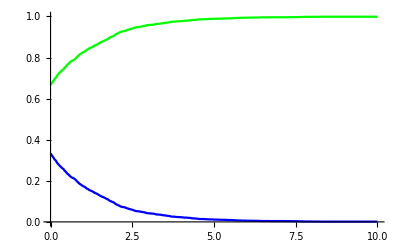

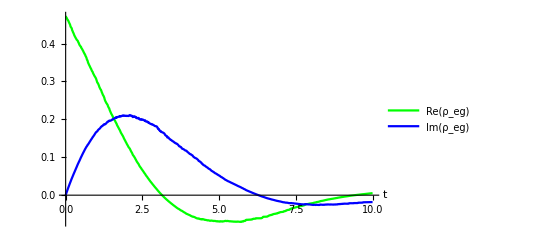

```mathematica
(* coherent dynamics *)
ListPlot[{Table[{n dt,Sum[Re[Conjugate[{0,1}.ψ[n,j]]{1,0}.ψ[n,j]],{j,1,num}]/num},{n,0,t/dt}],Table[{n dt,Sum[Im[Conjugate[{0,1}.ψ[n,j]]{1,0}.ψ[n,j]],{j,1,num}]/num},{n,0,t/dt}]},Joined->True,PlotRange->All,PlotStyle->{Green,Blue},AxesLabel->{Style["t",FontFamily->"Times New Roman",FontSize->14]},PlotLegends->{Style["Re(ρ_eg)",FontFamily->"Times New Roman"],Style["Im(ρ_eg)",FontFamily->"Times New Roman"]}]
```

## Quantum jump in cascade system

```mathematica
(*intial condition of state |ψ⟩={0,0,1}*)
Clear[c,t,Ω,δ,num,H]
c={{0,1,0},{0,0,1},{0,0,0}}; (*jumping operator representing decay channel*)
t=10;dt=0.01;
Ω=0.5; δ=0.1; (*Rabi freq & detuning*)
num=1000;
H={{0,Ω,0},{Ω,-δ,Ω},{0,Ω,-2δ}}-ⅈ/2 ConjugateTranspose[c].c;
```

```mathematica
Clear[ψ]
Monitor[Do[
ψ[0,j]={0,0,1};For[n=0,n≤t/dt,n++,If[Norm[c.ψ[n,j]]^2 dt>RandomReal[{0,1}],ψ[n+1,j]=(c.ψ[n,j])/Norm[c.ψ[n,j]],ψ[n+1,j]=(ψ[n,j]+H.ψ[n,j]dt)/Norm[ψ[n,j]+H.ψ[n,j]dt]]]
,{j,1,num}];,Row[{ProgressIndicator[j,{1,num}],j},""]]
Clear[n]
```

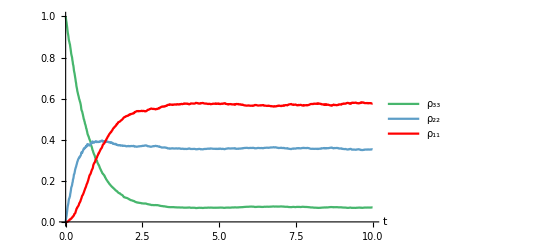

```mathematica
ListPlot[{Table[{n dt,Sum[Norm[{0,0,1}.ψ[n,j]]^2,{j,1,num}]/num},{n,0,t/dt}],Table[{n dt,Sum[Norm[{0,1,0}.ψ[n,j]]^2,{j,1,num}]/num},{n,0,t/dt}],Table[{n dt,Sum[Norm[{1,0,0}.ψ[n,j]]^2,{j,1,num}]/num},{n,0,t/dt}]},Joined->True,PlotRange->All,PlotStyle->{RGBColor[0.28026441037696703,0.715,0.4292089322474965],RGBColor[0.363898,0.618501,0.782349],Red},AxesLabel->{Style["t",FontFamily->"Times New Roman",FontSize->14]},PlotLegends->{Style["ρ_33",FontFamily->"Times New Roman"],Style["ρ_22",FontFamily->"Times New Roman"],Style["ρ_11",FontFamily->"Times New Roman"]}]
```

```mathematica
(* final population *)
tn=IntegerPart[t/dt];
Sum[Norm[{0,0,1}.ψ[tn,j]]^2,{j,1,num}]/num
Sum[Norm[{0,1,0}.ψ[tn,j]]^2,{j,1,num}]/num
Sum[Norm[{1,0,0}.ψ[tn,j]]^2,{j,1,num}]/num
Clear[tn]
```

0.0702018

0.353176

0.576623

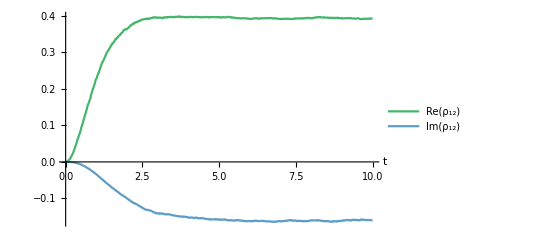

```mathematica
(* coherent dynamics *)
ListPlot[{Table[{n dt,Sum[Re[Conjugate[{1,0,0}.ψ[n,j]]{0,1,0}.ψ[n,j]],{j,1,num}]/num},{n,0,t/dt}],Table[{n dt,Sum[Im[Conjugate[{1,0,0}.ψ[n,j]]{0,1,0}.ψ[n,j]],{j,1,num}]/num},{n,0,t/dt}]},Joined->True,PlotRange->All,PlotStyle->{RGBColor[0.28026441037696703,0.715,0.4292089322474965],RGBColor[0.363898,0.618501,0.782349]},AxesLabel->{Style["t",FontFamily->"Times New Roman",FontSize->14]},PlotLegends->{Style["Re(ρ_12)",FontFamily->"Times New Roman"],Style["Im(ρ_12)",FontFamily->"Times New Roman"]}]
```

```mathematica
(* final coherence *)
tn=IntegerPart[t/dt];
Sum[Conjugate[{1,0,0}.ψ[999,j]]{0,1,0}.ψ[999,j],{j,1,num}]/num
Clear[tn]
```

0.392144-0.159649 ⅈ